```mathematica
ClearAll["Global`*"]
```

```mathematica
m[ n_, d_] := m[n,d]=d Sum[ 1 - m[n/j, d], {j,1+d, n, d}]
```

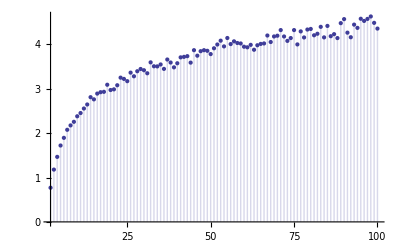

```mathematica
DiscretePlot[ m[n,1/8],{n,2,100}]
```

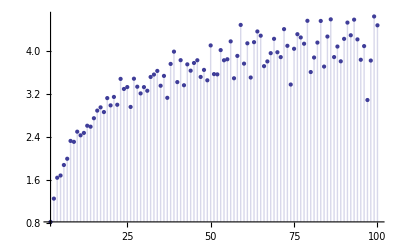

```mathematica
DiscretePlot[ m[n,1/4],{n,2,100}]
```

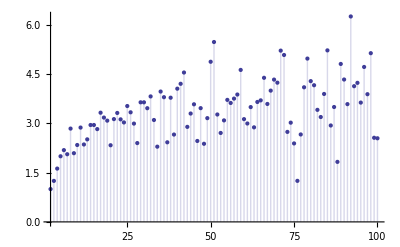

```mathematica
DiscretePlot[ m[n,1/2],{n,2,100}]
```

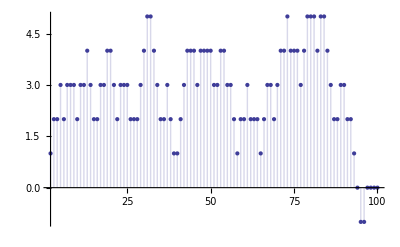

```mathematica
DiscretePlot[ m[n,1],{n,2,100}]
```

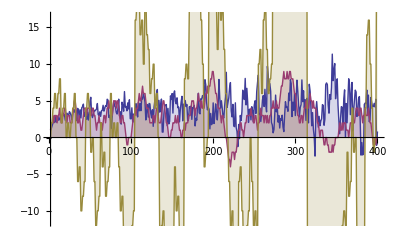

```mathematica
DiscretePlot[ {m[n, .5], m[n, 1], m[n, 2]}, {n, 2, 400}]
```

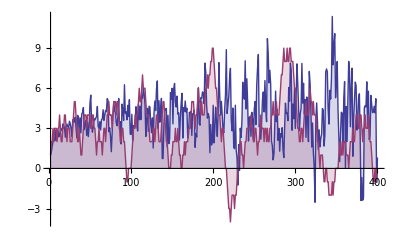

```mathematica
DiscretePlot[ {m[n, .5], m[n, 1]}, {n, 2, 400}]
```

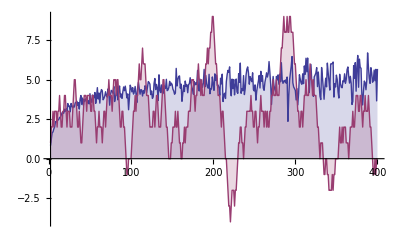

```mathematica
DiscretePlot[ {m[n, .25], m[n, 1]}, {n, 2, 400}]
```

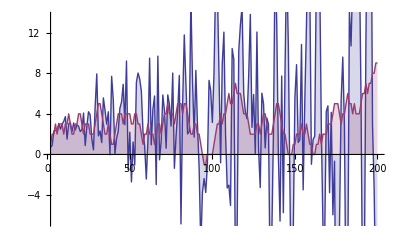

```mathematica
DiscretePlot[ {m[n, .7], m[n, 1]}, {n, 2, 200}]
```

```mathematica
p[ n_, k_, d_] := p[n,k,d]=d Sum[ 1/k - p[n/j, k+1, d], {j,1+d, n, d}]
```

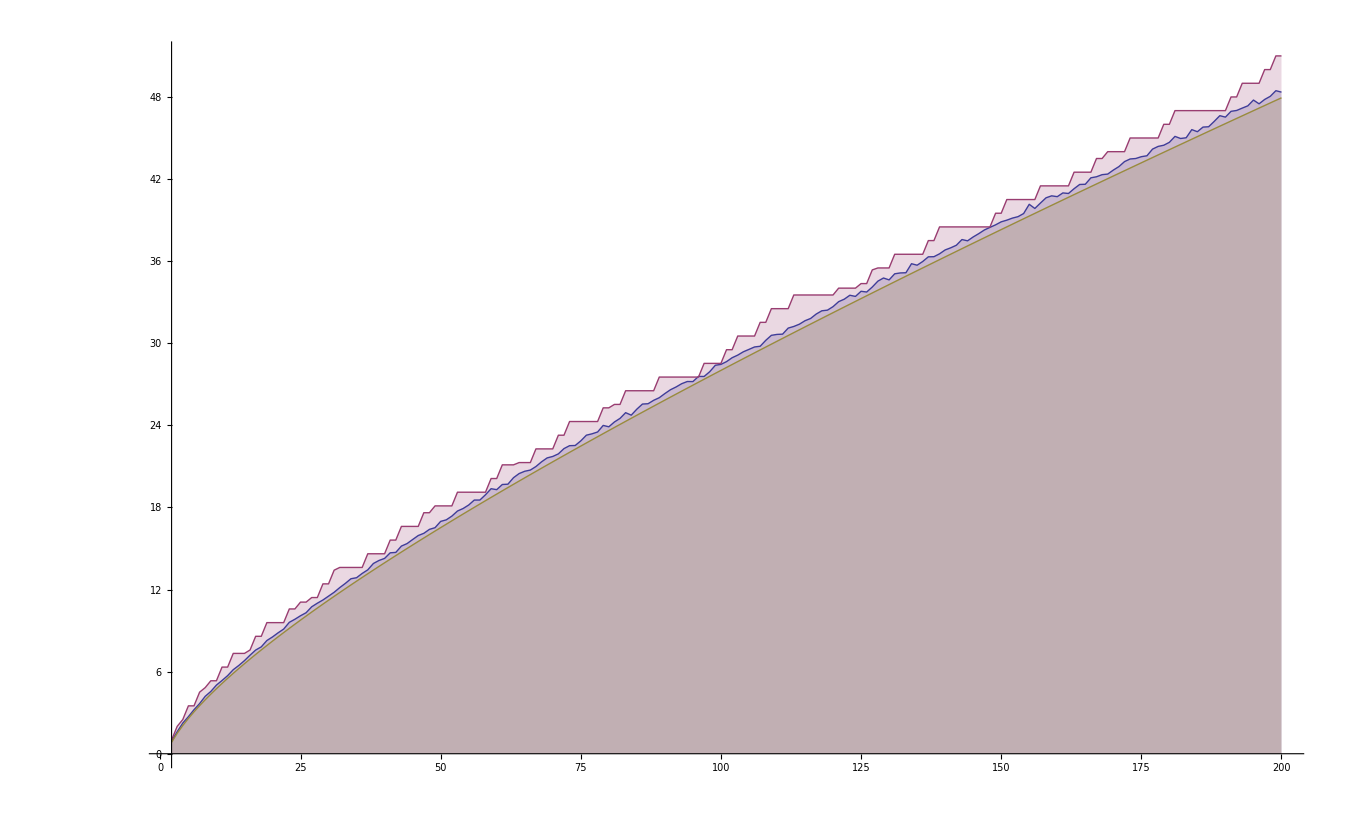

```mathematica
DiscretePlot[ {p[n, 1, .25],p[n,1, 1], LogIntegral[n]-Log[Log[n]]-EulerGamma}, {n, 2, 200}]
```

0.0004

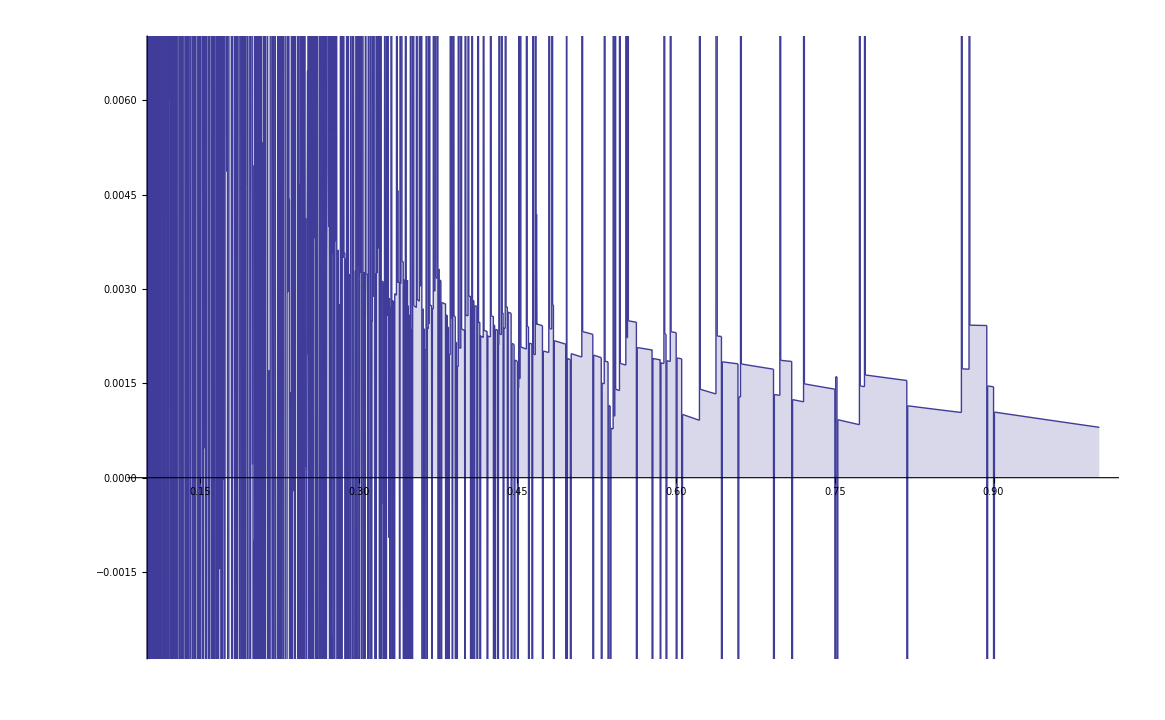

```mathematica
a = .0004
DiscretePlot[ {p[10, 1, n] - p[10, 1, n-a] }, {n, .1,1, a}]
```